# Practical 1 Plotting of n^throots of Unity

### Submitted By- Puranjyoti Bera (20201043)

Q1. Plotting cube roots of unity.

n=3

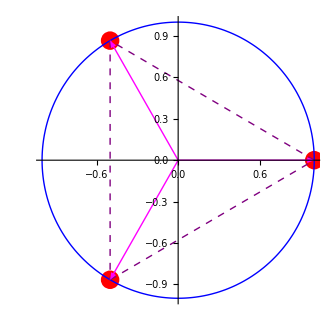

```mathematica
a:=ListPlot[Table[{Re[Exp[2*Pi*I*n/3]], Im[Exp[2*Pi*I*n/3]]},{n,0,2}],
AspectRatio-> Automatic,PlotStyle->{Red,PointSize[0.04]}];
b:=ParametricPlot[{Cos[t],Sin[t]},{t,0,2*Pi},PlotStyle->{Thick,Blue}];
c:=Table[Graphics[{Thick,Magenta,Arrow[{{0,0},{Re[Exp[2*Pi*I*n/3]],Im[Exp[2*Pi*I*n/3]]}}]}],{n,0,2}];
d:=Table[Graphics[{Thick,Dashed,Purple,Line[{{Re[Exp[2*Pi*I*n/3]],Im[Exp[2*Pi*I*n/3]]},{Re[Exp[2*Pi*I(n+1)/3]],Im[Exp[2*Pi*I*(n+1)/3]]}}]}],{n,0,2}];

Show[a,b,c,d,PlotRange->1.25]
```

Q2. Plotting 4^th roots of unity.

n=4

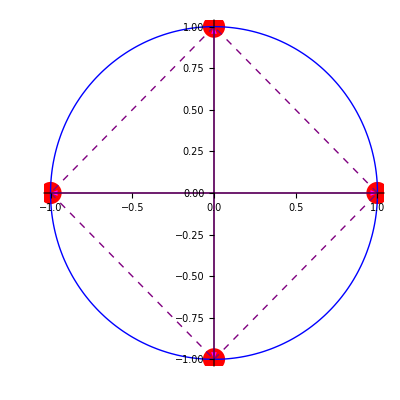

```mathematica
a:=ListPlot[Table[{Re[Exp[2*Pi*I*n/4]], Im[Exp[2*Pi*I*n/4]]},{n,0,3}],
AspectRatio-> Automatic,PlotStyle->{Red,PointSize[0.04]}];
b:=ParametricPlot[{Cos[t],Sin[t]},{t,0,2*Pi},PlotStyle->{Thick,Blue}];
c:=Table[Graphics[{Thick,Magenta,Arrow[{{0,0},{Re[Exp[2*Pi*I*n/4]],Im[Exp[2*Pi*I*n/4]]}}]}],{n,0,3}];
d:=Table[Graphics[{Thick,Dashed,Purple,Line[{{Re[Exp[2*Pi*I*n/4]],Im[Exp[2*Pi*I*n/4]]},{Re[Exp[2*Pi*I(n+1)/4]],Im[Exp[2*Pi*I*(n+1)/4]]}}]}],{n,0,3}];

Show[a,b,c,d,PlotRange->1.25]
```

Q3. Plotting 5^th roots of unity.

n=5

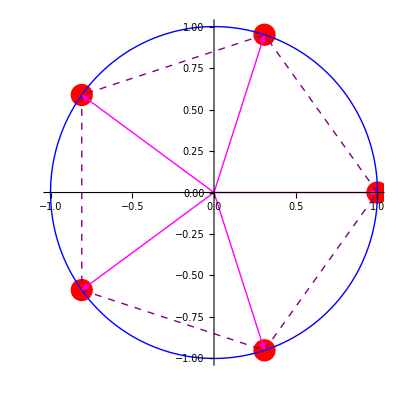

```mathematica
a:=ListPlot[Table[{Re[Exp[2*Pi*I*n/5]], Im[Exp[2*Pi*I*n/5]]},{n,0,4}],
AspectRatio-> Automatic,PlotStyle->{Red,PointSize[0.04]}];
b:=ParametricPlot[{Cos[t],Sin[t]},{t,0,2*Pi},PlotStyle->{Thick,Blue}];
c:=Table[Graphics[{Thick,Magenta,Arrow[{{0,0},{Re[Exp[2*Pi*I*n/5]],Im[Exp[2*Pi*I*n/5]]}}]}],{n,0,4}];
d:=Table[Graphics[{Thick,Dashed,Purple,Line[{{Re[Exp[2*Pi*I*n/5]],Im[Exp[2*Pi*I*n/5]]},{Re[Exp[2*Pi*I(n+1)/5]],Im[Exp[2*Pi*I*(n+1)/5]]}}]}],{n,0,4}];

Show[a,b,c,d,PlotRange->1.25]
```

Q4. Plotting 6^th roots of unity.

n=6

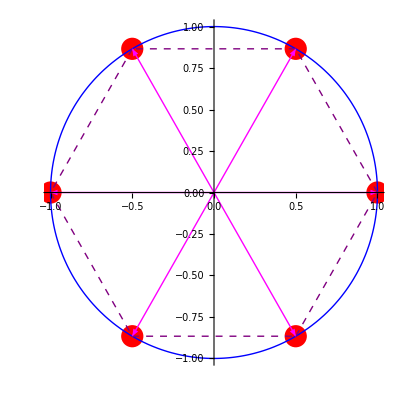

```mathematica
a:=ListPlot[Table[{Re[Exp[2*Pi*I*n/6]], Im[Exp[2*Pi*I*n/6]]},{n,0,5}],
AspectRatio-> Automatic,PlotStyle->{Red,PointSize[0.04]}];
b:=ParametricPlot[{Cos[t],Sin[t]},{t,0,2*Pi},PlotStyle->{Thick,Blue}];
c:=Table[Graphics[{Thick,Magenta,Arrow[{{0,0},{Re[Exp[2*Pi*I*n/6]],Im[Exp[2*Pi*I*n/6]]}}]}],{n,0,5}];
d:=Table[Graphics[{Thick,Dashed,Purple,Line[{{Re[Exp[2*Pi*I*n/6]],Im[Exp[2*Pi*I*n/6]]},{Re[Exp[2*Pi*I(n+1)/6]],Im[Exp[2*Pi*I*(n+1)/6]]}}]}],{n,0,5}];

Show[a,b,c,d,PlotRange->1.25]
```

Q5. Plotting 7^th roots of unity.

n=7

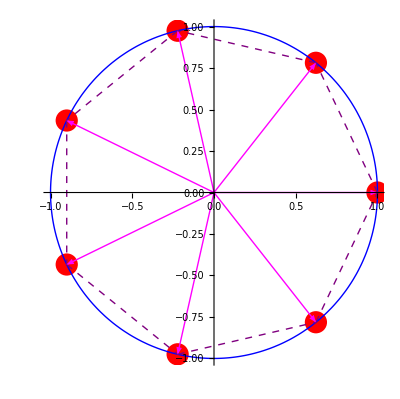

```mathematica
a:=ListPlot[Table[{Re[Exp[2*Pi*I*n/7]], Im[Exp[2*Pi*I*n/7]]},{n,0,6}],
AspectRatio-> Automatic,PlotStyle->{Red,PointSize[0.04]}];
b:=ParametricPlot[{Cos[t],Sin[t]},{t,0,2*Pi},PlotStyle->{Thick,Blue}];
c:=Table[Graphics[{Thick,Magenta,Arrow[{{0,0},{Re[Exp[2*Pi*I*n/7]],Im[Exp[2*Pi*I*n/7]]}}]}],{n,0,6}];
d:=Table[Graphics[{Thick,Dashed,Purple,Line[{{Re[Exp[2*Pi*I*n/7]],Im[Exp[2*Pi*I*n/7]]},{Re[Exp[2*Pi*I(n+1)/7]],Im[Exp[2*Pi*I*(n+1)/7]]}}]}],{n,0,6}];

Show[a,b,c,d,PlotRange->1.25]
```

Q6. Plotting 8^th roots of unity.

n=8

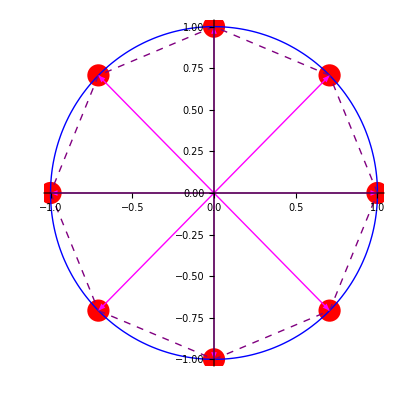

```mathematica
a:=ListPlot[Table[{Re[Exp[2*Pi*I*n/8]], Im[Exp[2*Pi*I*n/8]]},{n,0,7}],
AspectRatio-> Automatic,PlotStyle->{Red,PointSize[0.04]}];
b:=ParametricPlot[{Cos[t],Sin[t]},{t,0,2*Pi},PlotStyle->{Thick,Blue}];
c:=Table[Graphics[{Thick,Magenta,Arrow[{{0,0},{Re[Exp[2*Pi*I*n/8]],Im[Exp[2*Pi*I*n/8]]}}]}],{n,0,7}];
d:=Table[Graphics[{Thick,Dashed,Purple,Line[{{Re[Exp[2*Pi*I*n/8]],Im[Exp[2*Pi*I*n/8]]},{Re[Exp[2*Pi*I(n+1)/8]],Im[Exp[2*Pi*I*(n+1)/8]]}}]}],{n,0,7}];

Show[a,b,c,d,PlotRange->1.25]
```